```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_7"];

LNDatabeta089=ReadList["LNData_NM_beta_0.89.txt"];
LNDatabeta090=ReadList["LNData_NM_beta_0.9.txt"];
LNDatabeta091=ReadList["LNData_NM_beta_0.91.txt"];
LNDatabeta092=ReadList["LNData_NM_beta_0.92.txt"];
LNDatabeta093=ReadList["LNData_NM_beta_0.93.txt"];
LNDatabeta094=ReadList["LNData_NM_beta_0.94.txt"];
LNDatabeta095=ReadList["LNData_NM_beta_0.95.txt"];
LNDatabeta096=ReadList["LNData_NM_beta_0.96.txt"];
LNDatabeta097=ReadList["LNData_NM_beta_0.97.txt"];
LNDatabeta098=ReadList["LNData_NM_beta_0.98.txt"];
LNDatabeta099=ReadList["LNData_NM_beta_0.99.txt"];
```

```mathematica
MeanBetaData={
{0.89, Mean[Table[LNDatabeta089[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.90, Mean[Table[LNDatabeta090[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.91, Mean[Table[LNDatabeta091[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.92, Mean[Table[LNDatabeta092[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.93, Mean[Table[LNDatabeta093[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.94, Mean[Table[LNDatabeta094[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.95, Mean[Table[LNDatabeta095[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.96, Mean[Table[LNDatabeta096[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.97, Mean[Table[LNDatabeta097[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.98, Mean[Table[LNDatabeta098[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.99, Mean[Table[LNDatabeta099[[1]][[pt]][[2]], {pt, 100, 1001}]]}
};
```

```mathematica
(* LN12 and LN34 Data *)
LNBetaData={
{LNDatabeta089[[1]], LNDatabeta089[[6]], 0.89},
{LNDatabeta090[[1]], LNDatabeta090[[6]], 0.90},
{LNDatabeta091[[1]], LNDatabeta091[[6]], 0.91},
{LNDatabeta092[[1]], LNDatabeta092[[6]], 0.92},
{LNDatabeta093[[1]], LNDatabeta093[[6]], 0.93},
{LNDatabeta094[[1]], LNDatabeta094[[6]], 0.94},
{LNDatabeta095[[1]], LNDatabeta095[[6]], 0.95},
{LNDatabeta096[[1]], LNDatabeta096[[6]], 0.96},
{LNDatabeta097[[1]], LNDatabeta097[[6]], 0.97},
{LNDatabeta098[[1]], LNDatabeta098[[6]], 0.98},
{LNDatabeta099[[1]], LNDatabeta099[[6]], 0.99}};
```

```mathematica
(* Plotting Properties *)
width=600;
height=300;
PlotFormat1={LabelStyle->Directive[18], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
LabelingInfo1={AxesLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, β, η=0, m=1, ω=7, Ω=7, γ=0.5"};
LabelingInfo2={AxesLabel->{"τ", "ℒ𝒩"}};
```

```mathematica
(* LN12 and LN34 Plot as a function of β *)
LNBetaPlots=Table[ListPlot[{LNBetaData[[betavalue]][[1]], LNBetaData[[betavalue]][[2]]}, Joined->True, Evaluate[PlotFormat1], Evaluate[LabelingInfo2], PlotLabel->"n=4, β="<>ToString[LNBetaData[[betavalue]][[3]]]<>", η=0, m=1, ω=7, Ω=7, γ=0.5}"], {betavalue, 1, Length[LNBetaData]}];
ListAnimate[LNBetaPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

InterpolatingFunction[…]

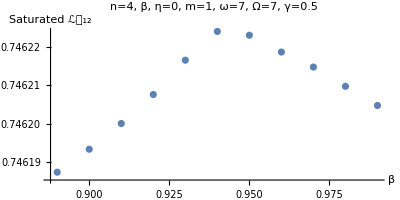
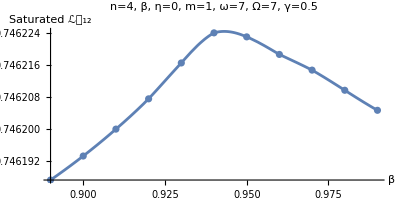

```mathematica
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Interpolation: Must zoom in to where the suspected maximum is. *)
iMeanBetafunc=Interpolation[MeanBetaData]
iMeanBetaDatalinePlot=Plot[iMeanBetafunc[x], {x, 0.89, 0.99}, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show together *)
Row[{MeanBetaDataptPlotZoom, Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom]}]
```

```mathematica
(* Take the derivative of the Interpolation Function *)
derivfunc[β_]:=D[iMeanBetafunc[x], x]/.x->β
(* Calculating the value of the derivative of Interpolation Function near the maximum. Get start and end values from the graph. *)
start= 0.935;
end=0.950;
deridata=Table[{β, derivfunc[β]}, {β, start, end, 10^-6}];
```

{0.943113,0.746224}

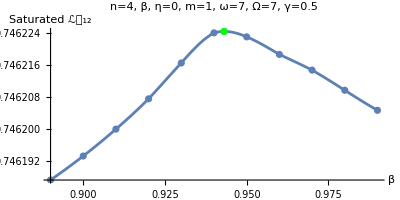

```mathematica
(* Finding Optimum β for when Ω=ω=6 *)
βmax={};
Table[If[deridata[[value]][[2]]>0 && deridata[[value+1]][[2]]<0, AppendTo[βmax, Mean[{deridata[[value]][[1]],deridata[[value+1]][[1]]}]]], {value, 1, Length[deridata]-1}];
optimumpt=Flatten[{βmax, iMeanBetafunc[βmax]}]
(* Plot {βmax, Saturated LN12} *)
optimumptPlot=ListPlot[{optimumpt}, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotStyle->Green];
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom, optimumptPlot]
```